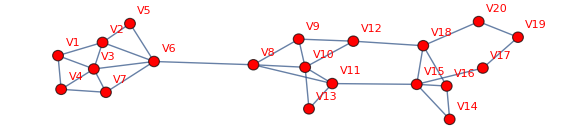

```mathematica
(**************************************************** Task 1.1 ***********************)
edges={
V1<->V2,V1<->V3,V1<->V4,V2<->V3,V2<->V5,V2<->V6,V3<->V4,V3<->V6,V3<->V7,V4<->V7,V5<->V6,V6<->V7,
V8<->V9,V8<->V10,V8<->V11,V9<->V10,V9<->V12,V10<->V11,V10<->V12,V10<->V13,V11<->V13,
V14<->V15,V14<->V16,V15<->V16,V15<->V17,V15<->V18,V16<->V18,V17<->V19,V18<->V20,V19<->V20,

V6<->V8,V11<->V15,V12<->V18 };

 
g=Graph[edges,VertexLabels->"Name",GraphLayout->"SpringElectricalEmbedding",ImageSize->Large,EdgeStyle->{Thick}
, VertexSize->Large, VertexStyle->Red]
```

```mathematica
(**************************************************** Task 1.2 ***********************)
```

```mathematica
adjacencyMatrix = AdjacencyMatrix[g];
degreeMatrix=DiagonalMatrix[Total[adjacencyMatrix,{2}]];
laplacianMatrix=degreeMatrix-adjacencyMatrix;
MatrixForm[laplacianMatrix]
```

(3 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 4 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | -1 | 5 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | -1 | 3 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 2 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | -1 | 0 | -1 | 5 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | -1 | 0 | -1 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 4 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 3 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 5 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 4 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -1 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 5 | -1 | -1 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 3 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 2 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 4 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 2 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 2)

```mathematica
(**************************************************** Task 1.3 ***********************)
{eigenvalues,eigenvectors}=N[Eigensystem[laplacianMatrix]];
eigenvalues;
eigenvectors;
```

```mathematica
(**************************************************** Task 1.4 ***********************)
k = 20;
```

```mathematica
(**************************************************** Task 1.5 ***********************)
eigenpairs=Transpose[{eigenvalues,eigenvectors}];

sortedEigenpairs=SortBy[eigenpairs,First];

smallestFourVectors=Transpose[sortedEigenpairs[[;;k,2]]];

V = MatrixForm[smallestFourVectors];
```

```mathematica
(**************************************************** Task 1.6 ***********************)
clusters=FindClusters[smallestFourVectors,k];
```

```mathematica
(**************************************************** Task 1.7 ***********************)
vertices=VertexList[g];

clusterLabels=Table[With[{clusterIndex=Position[clusters,SelectFirst[clusters,MemberQ[#,smallestFourVectors[[i]]]&]]},If[clusterIndex==={},Missing[],First[First[clusterIndex]]]],{i,Length[vertices]}];

vertexColors=Table[ColorData["Rainbow"][clusterLabels[[i]]/Max[clusterLabels]],{i,Length[vertices]}];
```

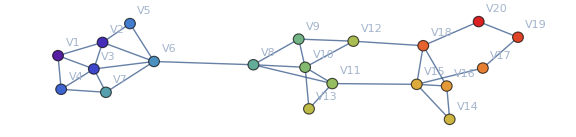

```mathematica
(**************************************************** Task 1.8 ***********************)
coloredGraph=
Graph[
vertices,
EdgeList[g],
VertexStyle->Thread[vertices->vertexColors],
VertexLabels->"Name",
VertexSize->Large,
EdgeStyle->Thick, 
ImageSize->Large
]
```

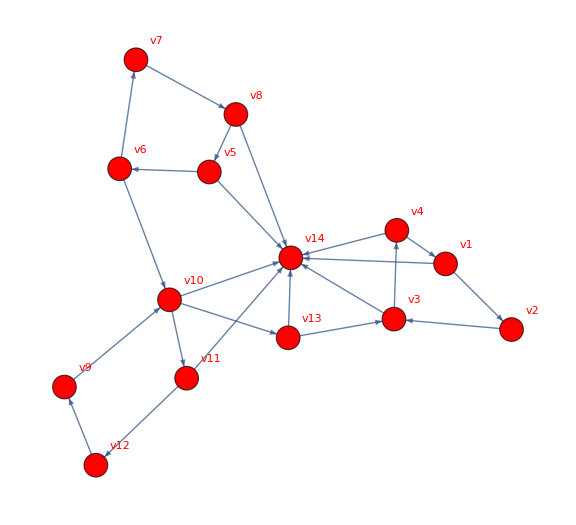

```mathematica
(**************************************************** Task 2.1 ***********************)
edges={v1->v2,v2->v3,v3->v4,v4->v1,v5->v6,v6->v7,v7->v8,v8->v5,v9->v10,v10->v11,v11->v12,v12->v9,v13->v14,v10->v13,v6->v10, v13 -> v3, v10 -> v14, v3 -> v14, v4 -> v14, v5 -> v14, v8 -> v14, v1 -> v14, v11 -> v14};
g=Graph[edges,VertexLabels->"Name", DirectedEdges->True,ImageSize->Large,EdgeStyle->Thick,VertexSize->Large,VertexStyle->Red]
```

```mathematica
(**************************************************** Task 2.2 ***********************)
vertices=VertexList[g];
n=Length[vertices];

adjMatrix=AdjacencyMatrix[g];
outDegree=Total[adjMatrix,{2}];

mMatrix=Table[If[outDegree[[j]]==0,1/n,adjMatrix[[i,j]]/outDegree[[j]]],{i,n},{j,n}];
mMatrix=Map[#/Total[#]&,mMatrix];
MatrixForm[mMatrix]
```

(0 | 14/15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/15
0 | 0 | 7/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8
0 | 0 | 0 | 7/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8
7/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8
0 | 0 | 0 | 0 | 0 | 7/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8
0 | 0 | 0 | 0 | 0 | 0 | 42/59 | 0 | 0 | 14/59 | 0 | 0 | 0 | 3/59
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7/8 | 0 | 0 | 0 | 0 | 0 | 1/8
0 | 0 | 0 | 0 | 7/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14/17 | 0 | 0 | 0 | 3/17
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7/15 | 0 | 7/15 | 1/15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14/15 | 0 | 1/15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14/15 | 0 | 0 | 0 | 0 | 1/15
0 | 0 | 7/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
(**************************************************** Task 2.3 ***********************)
{eigenvalues,eigenvectors}=N[Eigensystem[mMatrix]];
eigenpairs=Transpose[{eigenvalues,eigenvectors}];
sortedEigenpairs=ReverseSort[eigenpairs,First];
biggerVectors=Transpose[sortedEigenpairs[[;;1,2]]];
vector=MatrixForm[biggerVectors]
```

(1.
1.
1.
1.
1.
1.
1.
1.
1.
1.
1.
1.
1.
1.)

```mathematica
(**************************************************** Task 2.4 ***********************)
ranks=PageRankCentrality[g];
vertexRanks=AssociationThread[VertexList[g]->ranks];
MatrixForm[vertexRanks//Normal]
```

(v1→0.050936
v2→0.0463998
v3→0.0867231
v4→0.0616093
v5→0.0513651
v6→0.0465822
v7→0.0445494
v8→0.062619
v9→0.0649428
v10→0.0997508
v11→0.0530147
v12→0.0472833
v13→0.0530147
v14→0.23121)